## Setup of functions we will need

```mathematica
$Assumptions=j>k>0&&γ>1
```

j>k>0&&γ>1

```mathematica
S[z_,w_]:=Conjugate[z].w
```

```mathematica
J[z_]:= Conjugate[{{0,1},{-1,0}}.z]
```

```mathematica
NN[ϕ_,θ_]:= {Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]}
```

```mathematica
SpinorN[{x_,y_,z_}]:=1/(√2){-(x-I y)/(√(1+z)),√(1+z)}
```

We write the Tγ along the z axis

```mathematica
Tγz[r_]=({{Cosh[r], γ Sinh[r], 0}, {- γ Sinh[r], Cosh[r], 0}, {0, 0, 1}})
```

{{Cosh[r],γ Sinh[r],0},{-γ Sinh[r],Cosh[r],0},{0,0,1}}

```mathematica
Tm1γz[r_]=({{Cosh[r], -1/γ Sinh[r], 0}, {1/γ Sinh[r], Cosh[r], 0}, {0, 0, 1}})
```

{{Cosh[r],-Sinh[r]/γ,0},{Sinh[r]/γ,Cosh[r],0},{0,0,1}}

## Boundary Data

Dihedral angles. Valid for j>k>0 no issues here

```mathematica
Reduce[1-k^2/j^2>0&&j>k>0]
```

k>0&&j>k

Equilateral tetrahedron

```mathematica
θe=1/2ArcCos[1/3];
```

```mathematica
n1=NN[π/2,π/2-θe]//FullSimplify
n2=NN[3/2 π,π/2-θe]//FullSimplify
n3=NN[0,π/2+θe]//FullSimplify
n4=NN[π,π/2+θe]//FullSimplify
```

{0,√(2/3),1/(√3)}

{0,-√(2/3),1/(√3)}

{√(2/3),0,-1/(√3)}

{-√(2/3),0,-1/(√3)}

```mathematica
k n1 + k n2 + k n3 + k n4
```

{0,0,0}

```mathematica
Cross[n2,n1]
```

{-(2 √2)/3,0,0}

Isosceles Tetrahedron

```mathematica
θ0=ArcCos[k/(Sqrt[3]j)];
```

```mathematica
nt1=NN[π/2,θ0]//FullSimplify
nt2=NN[π 3/2,θ0]//FullSimplify
nt3=NN[0,π-θ0]//FullSimplify
nt4=NN[π,π-θ0]//FullSimplify
```

{0,√(1-k^2/(3 j^2)),k/(√3 j)}

{0,-√(1-k^2/(3 j^2)),k/(√3 j)}

{√(1-k^2/(3 j^2)),0,-k/(√3 j)}

{-√(1-k^2/(3 j^2)),0,-k/(√3 j)}

```mathematica
j nt1 + j nt2 + j nt3 + j nt4
```

{0,0,0}

```mathematica
z={0,0,1}
```

{0,0,1}

We derive also the tilde frame vectors

we compute first the spinor ztilde and the frame vector for  the boundary data

```mathematica
zt1=SpinorN[nt1];
F1=Im[S[J[zt1],PauliMatrix[#].zt1]&/@Range[3]]//FullSimplify;
nF1=Re[S[J[zt1],PauliMatrix[#].zt1]&/@Range[3]]//FullSimplify;
```

```mathematica
zt2=SpinorN[nt2];
F2=Im[S[J[zt2],PauliMatrix[#].zt2]&/@Range[3]]//FullSimplify;
nF2=Re[S[J[zt2],PauliMatrix[#].zt2]&/@Range[3]]//FullSimplify;
```

```mathematica
zt3=SpinorN[nt3];
F3=Im[S[J[zt3],PauliMatrix[#].zt3]&/@Range[3]]//FullSimplify;
nF3=Re[S[J[zt3],PauliMatrix[#].zt3]&/@Range[3]]//FullSimplify;
```

```mathematica
zt4=SpinorN[nt4];
F4=Im[S[J[zt4],PauliMatrix[#].zt4]&/@Range[3]]//FullSimplify;
nF4=Re[S[J[zt4],PauliMatrix[#].zt4]&/@Range[3]]//FullSimplify;
```

```mathematica
z1=SpinorN[n1];
z2=SpinorN[n2];
z3=SpinorN[n3];
z4=SpinorN[n4];
```

## The solutions for the group element

The first solution is characterized by

```mathematica
r1=ArcSinh[Sqrt[j^2-k^2]/(k Sqrt[(1+γ^2)]Sqrt[(1-(z.n2)^2)])];
```

```mathematica
ψ1 =ArcCos[Cosh[r1]/(√(Cosh[r1]^2+γ^2 Sinh[r1]^2))];
```

Explicit  check that the boosted orientation equations are satisfied

```mathematica
Rzψ=RotationMatrix[ψ1,z]//FullSimplify;
```

```mathematica
Tγh = Rzψ.Tγz[r1]//FullSimplify;
```

```mathematica
Tγh.(k n1)==j nt1//FullSimplify
```

True

```mathematica
Tγh.(k n2)==j nt2//FullSimplify
```

True

```mathematica
Tγh.(k n3)==j nt3//FullSimplify
```

True

```mathematica
Tγh.(k n4)==j nt4//FullSimplify
```

True

The second solution is characterized by

```mathematica
r2=-ArcSinh[Sqrt[(j^2-k^2)/(k^2(1+γ^2)(1-(z.n2)^2))]];
```

```mathematica
ψ2=-ArcCos[Cosh[r2]/(√(Cosh[r2]^2+γ^2 Sinh[r2]^2))];
```

```mathematica
Rzψ2=RotationMatrix[ψ2,z]//FullSimplify;
```

Explicit  check that the boosted orientation equations are satisfied

```mathematica
Tγh2 = Rzψ2.Tγz[r2]//FullSimplify;
```

```mathematica
Tγh2.(k n1)==j nt1//FullSimplify
```

True

```mathematica
Tγh2.(k n2)==j nt2//FullSimplify
```

True

```mathematica
Tγh2.(k n3)==j nt3//FullSimplify
```

True

```mathematica
Tγh2.(k n4)==j nt4//FullSimplify
```

True

## The Flag phase at the first critical point

We use the formula derived in the paper to compute αt-βt

```mathematica
atmbt1=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F1+I nF1).Rzψ.(Cross[z,n1]/Norm[Cross[z,n1]])]//FullSimplify
atmbt2=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F2+I nF2).Rzψ.(Cross[z,n2]/Norm[Cross[z,n2]])]//FullSimplify
atmbt3=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F3+I nF3).Rzψ.(Cross[z,n3]/Norm[Cross[z,n3]])]//FullSimplify
atmbt4=Arg[j Sign[r1] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F4+I nF4).Rzψ.(Cross[z,n4]/Norm[Cross[z,n4]])]//FullSimplify
```

Arg[(-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

Arg[ⅈ (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

Arg[(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

## Vectorial phase and norm factor at the first critical point

The ratio of the norms is obtained from

```mathematica
logzoverhz21=Log[Cosh[r1]- z.n1 Sinh[r1]]//Simplify
logzoverhz22=Log[Cosh[r1]- z.n2 Sinh[r1]]//Simplify
logzoverhz23=Log[Cosh[r1]- z.n3 Sinh[r1]]//Simplify
logzoverhz24=Log[Cosh[r1]- z.n4 Sinh[r1]]//Simplify
```

Log[(-√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

Log[(-√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

Log[(√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

Log[(√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

```mathematica
υ[z2_]:=Arg[S[z2,SpinorN[z]]S[SpinorN[z],J[z2]]]
```

```mathematica
tαtmαmβ1= ArcTan[γ]+ υ[z1]+If[Sign[r1]>0,π,0]//FullSimplify
tαtmαmβ2= ArcTan[γ]+ υ[z2]+If[Sign[r1]>0,π,0]//FullSimplify
tαtmαmβ3= ArcTan[γ]+ υ[z3]+If[Sign[r1]>0,π,0]//FullSimplify
tαtmαmβ4= ArcTan[γ]+ υ[z4]+If[Sign[r1]>0,π,0]//FullSimplify
```

(3 π)/2+ArcTan[γ]

π/2+ArcTan[γ]

π+ArcTan[γ]

2 π+ArcTan[γ]

## Vectorial phase and norm factor at the second critical point

We use the formula derived in the paper to compute αt-βt

```mathematica
atmbt1b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F1+I nF1).Rzψ2.(Cross[z,n1]/Norm[Cross[z,n1]])]//FullSimplify
atmbt2b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F2+I nF2).Rzψ2.(Cross[z,n2]/Norm[Cross[z,n2]])]//FullSimplify
atmbt3b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F3+I nF3).Rzψ2.(Cross[z,n3]/Norm[Cross[z,n3]])]//FullSimplify
atmbt4b=Arg[j Sign[r2] Sqrt[1+γ^2]/Sqrt[j^2+γ^2 k^2] Exp[I ArcTan[γ k/j]] (F4+I nF4).Rzψ2.(Cross[z,n4]/Norm[Cross[z,n4]])]//FullSimplify
```

Arg[(j+ⅈ k γ) (ⅈ j+k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

Arg[(-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

Arg[-(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]

The ratio of the norms is obtained from

```mathematica
logzoverhz21b=Log[Cosh[r2]- z.n1 Sinh[r2]]//Simplify
logzoverhz22b=Log[Cosh[r2]- z.n2 Sinh[r2]]//Simplify
logzoverhz23b=Log[Cosh[r2]- z.n3 Sinh[r2]]//Simplify
logzoverhz24b=Log[Cosh[r2]- z.n4 Sinh[r2]]//Simplify
```

Log[(√(j^2-k^2)+√(3 j^2+k^2 (-1+2 γ^2)))/(√2 k √(1+γ^2))]

Log[(√(j^2-k^2)+√(3 j^2+k^2 (-1+2 γ^2)))/(√2 k √(1+γ^2))]

Log[-(√((j^2-k^2)/(1+γ^2)))/(√2 k)+√(1+(3 (j^2-k^2))/(2 k^2 (1+γ^2)))]

Log[-(√((j^2-k^2)/(1+γ^2)))/(√2 k)+√(1+(3 (j^2-k^2))/(2 k^2 (1+γ^2)))]

```mathematica
tαtmαmβ1b= ArcTan[γ]+ υ[z1]+If[Sign[r2]>0,π,0]//FullSimplify
tαtmαmβ2b= ArcTan[γ]+ υ[z2]+If[Sign[r2]>0,π,0]//FullSimplify
tαtmαmβ3b= ArcTan[γ]+ υ[z3]+If[Sign[r2]>0,π,0]//FullSimplify
tαtmαmβ4b= ArcTan[γ]+ υ[z4]+If[Sign[r2]>0,π,0]//FullSimplify
```

π/2+ArcTan[γ]

-π/2+ArcTan[γ]

ArcTan[γ]

π+ArcTan[γ]

## Action at the critical points

We focus on the first critical point

half-lowest spins strands. I am omitting the real part of the action!

```mathematica
strand1S=- I k tαtmαmβ1 + I j atmbt1 +  I γ k logzoverhz21
strand2S=- I k tαtmαmβ2 + I j atmbt2 +  I γ k logzoverhz22
strand3S= - I k tαtmαmβ3 + I j atmbt3 +  I γ k logzoverhz23
strand4S= - I k tαtmαmβ4 + I j atmbt4+  I γ k logzoverhz24
```

-ⅈ k ((3 π)/2+ArcTan[γ])+ⅈ j Arg[(-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[(-√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

-ⅈ k (π/2+ArcTan[γ])+ⅈ j Arg[ⅈ (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[(-√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

-ⅈ k (π+ArcTan[γ])+ⅈ j Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

-ⅈ k (2 π+ArcTan[γ])+ⅈ j Arg[(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

```mathematica
Action1 = strand1S+strand2S+strand3S+strand4S
```

-ⅈ k (π/2+ArcTan[γ])-ⅈ k (π+ArcTan[γ])-ⅈ k ((3 π)/2+ArcTan[γ])-ⅈ k (2 π+ArcTan[γ])+ⅈ j Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ j Arg[(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ j Arg[ⅈ (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ j Arg[(-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+2 ⅈ k γ Log[(-√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]+2 ⅈ k γ Log[(√(j^2-k^2)+k √(-1+(3 j^2)/k^2+2 γ^2))/(√2 k √(1+γ^2))]

At the second critical point

half-lowest spins strands. I am omitting the real part of the action!

```mathematica
strand1Sb=- I k tαtmαmβ1b + I j atmbt1b +  I γ k logzoverhz21b
strand2Sb=- I k tαtmαmβ2b + I j atmbt2b +  I γ k logzoverhz22b
strand3Sb= - I k tαtmαmβ3b + I j atmbt3b +  I γ k logzoverhz23b
strand4Sb= - I k tαtmαmβ4b + I j atmbt4b+  I γ k logzoverhz24b
```

-ⅈ k (π/2+ArcTan[γ])+ⅈ j Arg[(j+ⅈ k γ) (ⅈ j+k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+√(3 j^2+k^2 (-1+2 γ^2)))/(√2 k √(1+γ^2))]

-ⅈ k (-π/2+ArcTan[γ])+ⅈ j Arg[(-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[(√(j^2-k^2)+√(3 j^2+k^2 (-1+2 γ^2)))/(√2 k √(1+γ^2))]

-ⅈ k ArcTan[γ]+ⅈ j Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(√2 k)+√(1+(3 (j^2-k^2))/(2 k^2 (1+γ^2)))]

-ⅈ k (π+ArcTan[γ])+ⅈ j Arg[-(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(√2 k)+√(1+(3 (j^2-k^2))/(2 k^2 (1+γ^2)))]

```mathematica
Action2 = strand1Sb+strand2Sb+strand3Sb+strand4Sb
```

-ⅈ k ArcTan[γ]-ⅈ k (-π/2+ArcTan[γ])-ⅈ k (π/2+ArcTan[γ])-ⅈ k (π+ArcTan[γ])+ⅈ j Arg[(-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ j Arg[-(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ j Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+ⅈ j Arg[(j+ⅈ k γ) (ⅈ j+k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+2 ⅈ k γ Log[-(√((j^2-k^2)/(1+γ^2)))/(√2 k)+√(1+(3 (j^2-k^2))/(2 k^2 (1+γ^2)))]+2 ⅈ k γ Log[(√(j^2-k^2)+√(3 j^2+k^2 (-1+2 γ^2)))/(√2 k √(1+γ^2))]

The difference of the two actions at the critical points is given by

```mathematica
(Action1-Action2)//FullSimplify
```

-ⅈ (4 k π+j (-Arg[-(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]-Arg[(j+ⅈ k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+Arg[(-ⅈ j+k γ) (j-ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+Arg[-(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]-Arg[ⅈ (j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+Arg[(j+ⅈ k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]-Arg[(-ⅈ j+k γ) (j+ⅈ k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]+Arg[(j+ⅈ k γ) (ⅈ j+k γ √(((j-k) (j+k))/(3 j^2+k^2 (-1+2 γ^2))))]))

```mathematica
Mod[N[(Action1-Action2)/.{γ->6/5,j->2,k->1}],2π]
```

0.+0. ⅈ

remember that these are all phases defined up to 2π

## Numerical data for the coherent invariant with j=2 k=1 γ=6/5 with λ=1, ... , 80

```mathematica
data={-0.0004546827460074104+I*7.324531806557556*^-19,2.6732160937684147*^-5+I*-1.1146019547457785*^-19,-5.354326242861585*^-6+I*3.3011174297974515*^-20,1.845564193934069*^-6+I*-1.4815927682673457*^-20,-7.699561411012255*^-7+I*6.945277080064897*^-21,3.6528363508924885*^-7+I*-3.4765764322018255*^-21,-1.953340448518481*^-7+I*2.47234507647053*^-21,1.1445807886181773*^-7+I*-1.806346107361153*^-21,-7.141920835338207*^-8+I*1.17838458412076*^-21,4.6739526448881955*^-8+I*-7.944927153267584*^-22,-3.183666924831303*^-8+I*5.779861992506887*^-22,2.243102321384254*^-8+I*-3.9460036064649116*^-22,-1.6256272996166426*^-8+I*2.7711861044232367*^-22,1.2065424120682513*^-8+I*-2.5285585916654947*^-22,-9.140969725615465*^-9+I*2.593136166284365*^-22,7.0508374050087565*^-9+I*-2.4582243545119784*^-22,-5.5251756286780354*^-9+I*2.1139865361928995*^-22,4.390564215950715*^-9+I*-1.7243765529467782*^-22,-3.5326901851209582*^-9+I*1.395418749689137*^-22,2.8743994546173012*^-9+I*-1.1549007349423063*^-22,-2.362497125633001*^-9+I*9.86971499067059*^-23,1.9596107164186722*^-9+I*-8.600434932653063*^-23,-1.6390370939319871*^-9+I*7.462756299361759*^-23,1.3814005222893287*^-9+I*-6.332319314522115*^-23,-1.1724424356217324*^-9+I*5.2598772290950685*^-23,1.0015337529159923*^-9+I*-4.3816034238149933*^-23,-8.606566291343353*^-10+I*3.7856767490895613*^-23,7.436965455783422*^-10+I*-3.438502937539348*^-23,-6.459431045329503*^-10+I*3.22468238677554*^-23,5.637333805072075*^-10+I*-3.04248958864913*^-23,-4.94194012667574*^-10+I*2.8506346627108026*^-23,4.3505257894350184*^-10+I*-2.644264041580799*^-23,-3.8449817736103776*^-10+I*2.4205213009568957*^-23,3.410773580506596*^-10+I*-2.176048303681868*^-23,-3.0361572290508364*^-10+I*1.9207764306057173*^-23,2.711583484696412*^-10+I*-1.6801757721379077*^-23,-2.4292414245491796*^-10+I*1.482532994072047*^-23,2.182706057129778*^-10+I*-1.3428824662368266*^-23,-1.96666429733147*^-10+I*1.2550220378644218*^-23,1.7767004091155339*^-10+I*-1.1966157424151695*^-23,-1.6091269174915124*^-10+I*1.1427178562919692*^-23,1.4608505318592246*^-10+I*-1.0777762078448498*^-23,-1.3292652086053288*^-10+I*9.99481716920105*^-24,1.2121663846414128*^-10+I*-9.149460475088953*^-24,-1.1076818259933559*^-10+I*8.341998219604697*^-24,1.014215591080508*^-10+I*-7.652243587576056*^-24,-9.304024026219946*^-11+I*7.114996208886338*^-24,8.55070323786829*^-11+I*-6.716562846804004*^-24,-7.872100928570596*^-11+I*6.410019095184028*^-24,7.259498224101519*^-11+I*-6.141462679689115*^-24,-6.705340403294716*^-11+I*5.871678738041588*^-24,6.203062603708998*^-11+I*-5.58334634014734*^-24,-5.746944340768941*^-11+I*5.277526993343357*^-24,5.331987643992035*^-11+I*-4.9677583219820456*^-24,-4.953814626380257*^-11+I*4.674130549903363*^-24,4.6085811040894825*^-11+I*-4.41558297932086*^-24,-4.2929035201033407*^-11+I*4.201572942655938*^-24,4.0037969337720327*^-11+I*-4.027577176660666*^-24,-3.7386222453531604*^-11+I*3.877435518101464*^-24,3.495041152442905*^-11+I*-3.730738047717743*^-24,-3.2709775999626757*^-11+I*3.571383388730432*^-24,3.064584700069122*^-11+I*-3.393423500371586*^-24,-2.874216273083217*^-11+I*3.201891775984421*^-24,2.6984023032255965*^-11+I*-3.0086968103939895*^-24,-2.535827719868069*^-11+I*2.8262650985927776*^-24,2.3853140111307714*^-11+I*-2.6625310535256207*^-24,-2.2458032559223415*^-11+I*2.5193018086425192*^-24,2.116344226090236*^-11+I*-2.3935667111624787*^-24,-1.9960802647485078*^-11+I*2.2800490800797454*^-24,1.8842386921125987*^-11+I*-2.1736076388613927*^-24,-1.7801215279351336*^-11+I*2.0708281489858736*^-24,1.683097351230243*^-11+I*-1.9706128346713927*^-24,-1.5925941444744316*^-11+I*1.8738553408283366*^-24,1.5080929917567033*^-11+I*-1.7825869285798405*^-24,-1.4291225191369898*^-11+I*1.6990695464859025*^-24,1.3552539813467027*^-11+I*-1.6251294758546462*^-24,-1.2860969124113305*^-11+I*1.5617275704068783*^-24,1.2212952691897279*^-11+I*-1.5086687208532024*^-24,-1.1605240065363794*^-11+I*1.4644628492232603*^-24,1.1034860310735047*^-11+I*-1.4264856411453004*^-24};
```

```mathematica
listplot = ListLogLogPlot[Abs[data],PlotStyle->Darker[Red],PlotMarkers->{Automatic,14},ImageSize->1000,Ticks->{All,All},PlotRange->All,AxesLabel->{"λ","|I|"},LabelStyle->Directive[24,Black]];
powerlaw = LogLogPlot[6* 10^-4*λ^-4,{λ,1,80},PlotStyle->{Thickness[.004],Blue}];
```

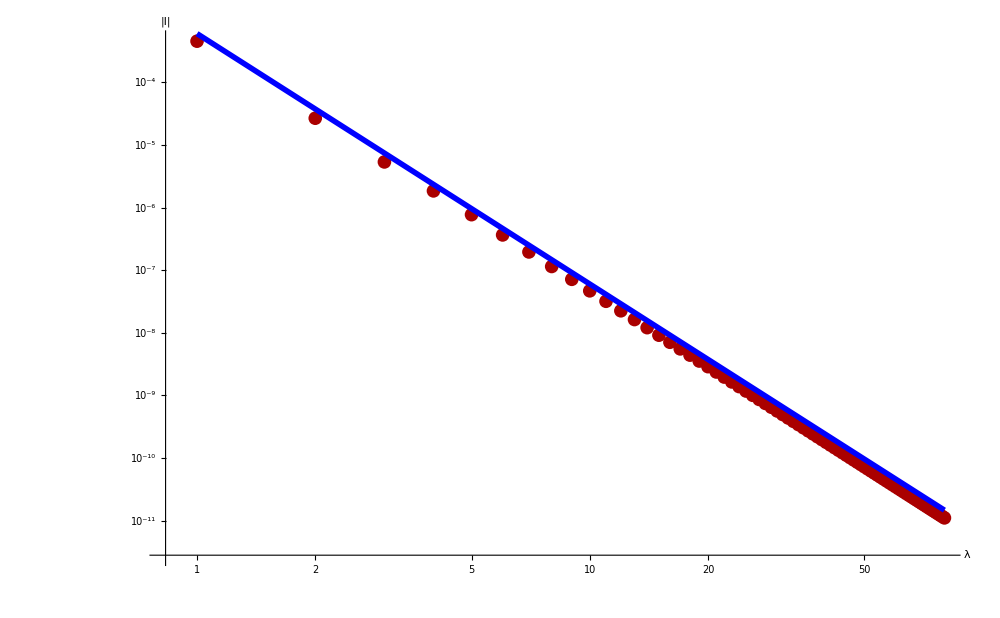

```mathematica
Show[listplot,powerlaw]
```